## Filtres BBD 32XX

Filtres correspondant au schéma de la datasheet

Valeurs numériques des composants :

```mathematica
AN={Subscript[R, 1]->120000.,Subscript[R, 2]->33000.,Subscript[R, 3]->120000.,Subscript[C, 1]->3.3 10^-9,Subscript[C, 2]->220. 10^-12,Subscript[R, 4]->56000.,Subscript[C, 3]->3.3 10^-9,Subscript[R, 5]->56000.,Subscript[C, 4]->3.3 10^-9,Subscript[R, 6]->33000.,Subscript[R, 7]->120000.,Subscript[C, 5]->220. 10^-12};
ANrounded={Subscript[R, 1]->120000.,Subscript[R, 2]->47000.,Subscript[R, 3]->120000.,Subscript[C, 1]->2.2 10^-9,Subscript[C, 2]->220. 10^-12,Subscript[R, 4]->56000.,Subscript[C, 3]->2.2 10^-9,Subscript[R, 5]->56000.,Subscript[C, 4]->2.2 10^-9,Subscript[R, 6]->33000.,Subscript[R, 7]->120000.,Subscript[C, 5]->220. 10^-12};
```

#### Filtre amont : 1ère partie

V_a est le potentiel au croisement de R1 (120k), C1 (3300pF), R2 (33k) et R3 (120k), cf partie gauche du montage dans la datasheet de la 3205 par exemple (tous les filtres sont les mêmes pour toutes les BBD : ils coupent tous autour de 3kHz ; et l'horloge étant au mini à 10kHz, c'est logique)
Vs = potentiel de sortie du premier AOp
On utilise la notation de Laplace (p = ⅈω)

```mathematica
eqKirchoff={(Subscript[V, in] - Subscript[V, a])/Subscript[R, 1]+(Subscript[V, s]-Subscript[V, a])/Subscript[R, 3]-Subscript[V, a]/Subscript[R, 2]==Subscript[V, a] p Subscript[C, 1] ,Subscript[V, a]/Subscript[R, 2]==-Subscript[V, s] Subscript[C, 2] p };
```

```mathematica
T1[p_]=Subscript[V, s]/.Solve[eqKirchoff,Subscript[V, s],Subscript[V, a]][[1]]/.Subscript[V, in]->1
```

```mathematica
T1[p_]=(Subscript[R, 3]/Subscript[R, 1])/(1+p Subscript[C, 2] ( Subscript[R, 2]+Subscript[R, 3]+Subscript[R, 2] Subscript[R, 3]/Subscript[R, 1])+p^2 Subscript[C, 1] Subscript[C, 2]  Subscript[R, 2] Subscript[R, 3]);
```

```mathematica
T1dB[ω_]=20 Log[Abs[T1[ⅈ ω]]];
```

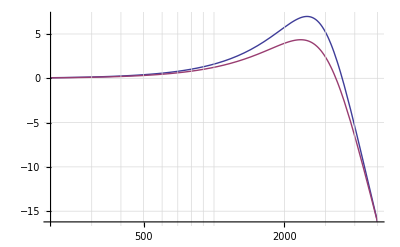

```mathematica
LogLinearPlot[{T1dB[ 2 π f]/.AN//Evaluate,T1dB[ 2 π f]/.ANrounded//Evaluate},{f,200,5000},PlotRange->All,GridLines->Automatic]
```

#### Filtre amont : 2ème partie

V_b : connection R4 (56k) avec C3 (3300pF) et R5 (56k)
V_c : connection R5 (56k) avec C4 (3300pF) et R6 (33k)
Vs = potentiel de sortie du second AOp
On utilise la notation de Laplace (p = ⅈω)

```mathematica
eqKirchoff2={(-Subscript[V, b]+Subscript[V, c])/Subscript[R, 5]+(-Subscript[V, b]+Subscript[V, in])/Subscript[R, 4]-Subscript[V, b] Subscript[C, 3] p==0,(Subscript[V, b]-Subscript[V, c])/Subscript[R, 5]-Subscript[V, c]/Subscript[R, 6]+(-Subscript[V, c]+Subscript[V, s])/Subscript[R, 7]-Subscript[V, c] Subscript[C, 4] p==0,Subscript[V, c]/Subscript[R, 6]==-Subscript[V, s] Subscript[C, 5] p};
```

```mathematica
T2[p_]=Subscript[V, s]/.Solve[eqKirchoff2,Subscript[V, s],{Subscript[V, c],Subscript[V, b]}]/.Subscript[V, in]->1//FullSimplify;
```

```mathematica
T2[p_]=Subscript[R, 7]/((Subscript[R, 5]+Subscript[R, 4] (1+p Subscript[C, 3] Subscript[R, 5])) (1+p Subscript[C, 5] Subscript[R, 6])+p Subscript[C, 5] (Subscript[R, 4]+Subscript[R, 5]+p Subscript[C, 3] Subscript[R, 4] Subscript[R, 5]+(1+p Subscript[C, 4] (Subscript[R, 4]+Subscript[R, 5])+p Subscript[C, 3] Subscript[R, 4] (1+p Subscript[C, 4] Subscript[R, 5])) Subscript[R, 6]) Subscript[R, 7]);
```

```mathematica
T2dB[ω_]=20 Log[Abs[T2[ⅈ ω]]]
```

{20 Log[Abs[R_7/((R_5+R_4 (1+ⅈ ω C_3 R_5)) (1+ⅈ ω C_5 R_6)+ⅈ ω C_5 (R_4+R_5+ⅈ ω C_3 R_4 R_5+(1+ⅈ ω C_4 (R_4+R_5)+ⅈ ω C_3 R_4 (1+ⅈ ω C_4 R_5)) R_6) R_7)]]}

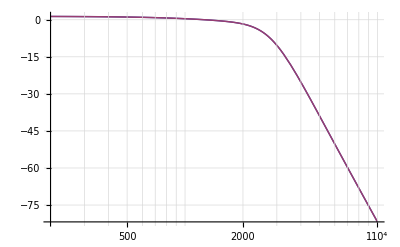

```mathematica
LogLinearPlot[{T2dB[ 2 π f]/.AN//Evaluate,T2dB[ 2 π f]/.ANrounded//Evaluate},{f,200,10000},PlotRange->All,GridLines->Automatic]
```

#### Filtre total amont :

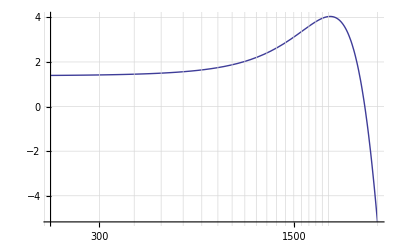

```mathematica
LogLinearPlot[T1dB[2 π f]+T2dB[ 2 π f]/.AN//Evaluate,{f,200,3000},PlotRange->All,GridLines->Automatic]
```

#### Filtre aval

V_A au croisement de R1 (43k), C1 (1800pF), R2 (39k)
V_b au croisement de R2(39k) R3(39k) et C2 (2.2n)
V_c au croisement de R3(39k) C3(2.7n) R4(33k) et R5 (120k)
Vs = potentiel de sortie de l'AOp
On utilise la notation de Laplace (p = ⅈω)

```mathematica
ANaval={Subscript[R, 1]->43000.,Subscript[R, 2]->39000.,Subscript[R, 3]->39000.,Subscript[C, 1]->1.8 10^-9,Subscript[C, 2]->2.2 10^-9,Subscript[R, 4]->33000.,Subscript[C, 3]->2.7 10^-9,Subscript[R, 5]->120000.,Subscript[C, 4]->220. 10^-12};
```

```mathematica
eqKirchoffAval={(Subscript[V, in] - Subscript[V, a])/Subscript[R, 1]+(Subscript[V, b]-Subscript[V, a])/Subscript[R, 2]-Subscript[V, a] Subscript[C, 1] p==0 ,(Subscript[V, a]-Subscript[V, b])/Subscript[R, 2]+(Subscript[V, c]-Subscript[V, b])/Subscript[R, 3]-Subscript[V, b] Subscript[C, 2] p==0,(Subscript[V, b]-Subscript[V, c])/Subscript[R, 3]+(Subscript[V, s]-Subscript[V, c])/Subscript[R, 5]+(-Subscript[V, c])/Subscript[R, 4]-Subscript[V, c] Subscript[C, 3] p==0,Subscript[V, c]/Subscript[R, 4]==-Subscript[V, s] Subscript[C, 4] p};
```

```mathematica
Taval[p_]=(Subscript[V, s]/.Solve[eqKirchoffAval,Subscript[V, s],{Subscript[V, a],Subscript[V, b],Subscript[V, c]}][[1]]/.Subscript[V, in]->1)//FullSimplify
```

1/(R_1 R_2 R_3 R_4 (p C_4 (-(-p C_1-1/R_1-1/R_2)/R_3^2-(1/R_2^2-(-p C_1-1/R_1-1/R_2) (-p C_2-1/R_2-1/R_3)) (-p C_3-1/R_3-1/R_4-1/R_5))+(1/R_2^2-(-p C_1-1/R_1-1/R_2) (-p C_2-1/R_2-1/R_3))/(R_4 R_5)))

```mathematica
TavaldB[ω_]=20 Log[Abs[Taval[ⅈ ω]]]
```

20 Log[Abs[1/(R_1 R_2 R_3 R_4 (ⅈ ω C_4 (-(-ⅈ ω C_1-1/R_1-1/R_2)/R_3^2-(1/R_2^2-(-ⅈ ω C_1-1/R_1-1/R_2) (-ⅈ ω C_2-1/R_2-1/R_3)) (-ⅈ ω C_3-1/R_3-1/R_4-1/R_5))+(1/R_2^2-(-ⅈ ω C_1-1/R_1-1/R_2) (-ⅈ ω C_2-1/R_2-1/R_3))/(R_4 R_5)))]]

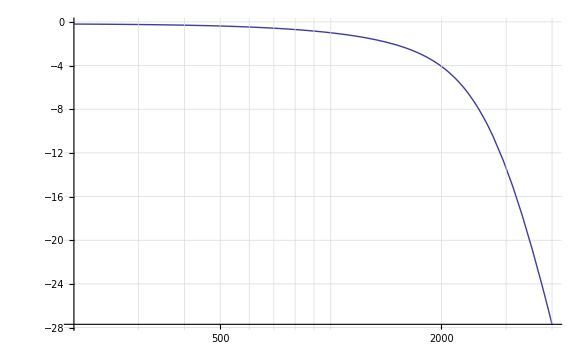

```mathematica
LogLinearPlot[TavaldB[ 2 π f]/.ANaval//Evaluate,{f,200,4000},PlotRange->All,GridLines->Automatic]
```

```mathematica
1
+p ((Subscript[C, 2] (Subscript[R, 1]+Subscript[R, 2]) Subscript[R, 3]+Subscript[C, 1] Subscript[R, 1] (Subscript[R, 2]+Subscript[R, 3])+Subscript[C, 4] ((Subscript[R, 1]+Subscript[R, 2]+Subscript[R, 3]) Subscript[R, 4]+(Subscript[R, 1]+Subscript[R, 2]+Subscript[R, 3]+Subscript[R, 4]) Subscript[R, 5]))/(Subscript[R, 1]+Subscript[R, 2]+Subscript[R, 3]))
+p^2 ((Subscript[C, 4] (Subscript[C, 3] (Subscript[R, 1]+Subscript[R, 2]+Subscript[R, 3]) Subscript[R, 4] Subscript[R, 5]+Subscript[C, 2] (Subscript[R, 1]+Subscript[R, 2]) (Subscript[R, 3] Subscript[R, 4]+(Subscript[R, 3]+Subscript[R, 4]) Subscript[R, 5]))+Subscript[C, 1] Subscript[R, 1] (Subscript[C, 2] Subscript[R, 2] Subscript[R, 3]+Subscript[C, 4] ((Subscript[R, 2]+Subscript[R, 3]) Subscript[R, 4]+(Subscript[R, 2]+Subscript[R, 3]+Subscript[R, 4]) Subscript[R, 5])))/(Subscript[R, 1]+Subscript[R, 2]+Subscript[R, 3]))
+p^3 ((Subscript[C, 4] (Subscript[C, 2] Subscript[C, 3] (Subscript[R, 1]+Subscript[R, 2]) Subscript[R, 3] Subscript[R, 4] Subscript[R, 5]+Subscript[C, 1] Subscript[R, 1] (Subscript[C, 3] (Subscript[R, 2]+Subscript[R, 3]) Subscript[R, 4] Subscript[R, 5]+Subscript[C, 2] Subscript[R, 2] (Subscript[R, 3] Subscript[R, 4]+(Subscript[R, 3]+Subscript[R, 4]) Subscript[R, 5]))))/(Subscript[R, 1]+Subscript[R, 2]+Subscript[R, 3]))
+p^4(Subscript[C, 1] Subscript[C, 2] Subscript[C, 3] Subscript[C, 4] Subscript[R, 1] Subscript[R, 2] Subscript[R, 3] Subscript[R, 4] Subscript[R, 5])/(Subscript[R, 1]+Subscript[R, 2]+Subscript[R, 3])
```

Calcul des pôles :

```mathematica
-1/Taval[p]/.ANaval//FullSimplify
```

5.07684×10^-18 (15174.+p) (40176.6+p) (3.2579×10^8+p (18930.8+p))

```mathematica
Solve[%==0,p]
```

{{p→-40176.6},{p→-15174.},{p→-9465.4-15368.7 ⅈ},{p→-9465.4+15368.7 ⅈ}}